Code developed for, and used in, the following publication, please cite appropriately:

Opening up baryon-number-violating operators
Julian Heeck, Diana Sokhashvili, Anil Thapa
arXiv:2603.17050
https://arxiv.org/abs/2603.17050

Related code and more information can also be found at
https://julian-heeck.github.io/BNV/

# Generate tree-level UV completions of non-derivative SMEFT operators

## Setup and auxiliary functions

Need Renato Fonseca’s GroupMath package from https://renatofonseca.net/groupmath. Please cite this package if you end up using this code for research purposes.

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.3 (19/December/2024)Author: Renato FonsecaReference: Comput. Phys. Commun. 267 (2021), 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

All particles form representations under (SU(2))_left(xSU(2))_rightx(SU(3))_color(xSU(2))_Lx(U(1))_Y, where hypercharge is related to electric charge Q by Q = T_3+Y.
(SU(2))_left(xSU(2))_right corresponds to the Lorentz group: scalars are (1,1) (i.e. singlets under (SU(2))_left(xSU(2))_right), left-handed fermions are (2,1), right-handed (1,2) (i.e. doublets under one of the SU(2)), and vectors are (2,2). In GroupMath, these representations are written using Dynkin coefficients, so an SU(2) singlet 1 is written as {0}, a doublet as {1}, a triplet at {2}, etc. An SU(3) triplet 3 is written as {1,0}, an anti-triplet OverBar[3]  as {0,1}, etc, see GroupMath documentation.

Standard Model particles (plus right-handed neutrinos NR):

```mathematica
group={SU2,SU2,SU3,SU2,U1};
singlet={{0},{0},{0,0},{0},0};
(*SU Subscript[(2), left] xSU Subscript[(2), right] xSU Subscript[(3), color] xSU Subscript[(2), L] xU Subscript[(1), Y] Standard Model fields:*)
H={{0},{0},{0,0},{1},1/2};
Q={{1},{0},{1,0},{1},1/6};
L={{1},{0},{0,0},{1},-1/2};
uR={{0},{1},{1,0},{0},2/3};
dR={{0},{1},{1,0},{0},-1/3};
eR={{0},{1},{0,0},{0},-1};
NR={{0},{1},{0,0},{0},0};
(*define anti-particle F^c fields, which have opposite chirality and opposite gauge quantum numbers:*)
Hc={{0},{0},{0,0},{1},-1/2};
Qc={{0},{1},{0,1},{1},-1/6};
Lc={{0},{1},{0,0},{1},1/2};
uc={{1},{0},{0,1},{0},-2/3};
dc={{1},{0},{0,1},{0},1/3};
ec={{1},{0},{0,0},{0},1};
Nc={{1},{0},{0,0},{0},0};
```

Some useful functions used later on:

```mathematica
(*replace SM particle quantum numbers by their names for display purposes:*)
ReplaceSMnames={Q->"Q",L->"L",uR->"uR",dR->"dR",eR->"eR",NR->"NR",Qc->"Qc",Lc->"Lc",uc->"uc",dc->"dc",ec->"ec",Nc->"Nc",H->"H",Hc->"Hc"};
InverseReplaceSMnames={"Q"->Q,"L"->L,"uR"->uR,"dR"->dR,"eR"->eR,"NR"->NR,"Qc"->Qc,"Lc"->Lc,"uc"->uc,"dc"->dc,"ec"->ec,"Nc"->Nc,"H"->H,"Hc"->Hc};

(*function that checks if a product of representations, e.g. an operator or vertex, contains a singlet, e.g. ContainsSinglet[{H,Hc}] = True, ContainsSinglet[{Lc,L}] = False*)
ContainsSinglet[reps_]:=MemberQ[Flatten[Drop[ReduceRepProduct[group,reps,UseName->False],None,-1],1],singlet]

(*function that multiplies representations and throws away multiplicities and all terms with spin > 1, e.g.  MyReduceRepProduct[{Lc,H,eR}] = {{{0},{0},{0,0},{2},0},{{0},{0},{0,0},{0},0}}. This will determine the representations of internal particles at each vertex. 
To also throw away internal vector particles, just change 1<x[[1,1]]||1<x[[2,1]] to 1<x[[1,1]]||1<x[[2,1]]||1<x[[1,1]]+x[[2,1]]*)
MyReduceRepProduct[reps_]:=DeleteCases[Flatten[Drop[ReduceRepProduct[group,reps,UseName->False],None,-1],1],x_/;1<x[[1,1]]||1<x[[2,1]]]

(*takes a list of particles, i.e. an 'operator', and creates all permutations so that scalars are always in the first slots; for example, MyPermutations[{H,L,H,L}] just gives {{H,H,L,L}}, but MyPermutations[{L,Q,H}] gives {{H,L,Q},{H,Q,L}}*)
MyPermutations[operator_]:=Flatten[#,1]&/@Tuples[{Permutations[Select[operator,MemberQ[{H,Hc},#]&]],Permutations[Select[operator,!MemberQ[{H,Hc},#]&]]}]


(* code that implements our definition of internal particle vs antiparticle. We define particles to have an unbarred SU(3) representation or, for real SU(3) reps, positive hypercharge:*)
  
(*SU(3) reps up to dimension 150 with a bar in its name (just GroupMath's Complement[RepsUpToDimN[SU3,150],RepsUpToDimNNoConjugates[SU3,150]]):*)
SU3antireps={{0,1},{0,3},{0,4},{0,6},{0,7},{0,9},{0,10},{0,12},{0,13},{0,15},{1,2},{1,4},{1,5},{1,7},{1,8},{1,10},{2,0},{2,3},{2,5},{2,6},{3,1},{3,4},{4,2},{5,0},{5,3},{6,1},{7,2},{8,0},{9,1},{11,0},{14,0}};
(*same as ConjugateIrrep[{SU3,SU2,U1},rep] but without need for GroupMath. Works with full Subscript[SU(2), left] Subscript[xSU(2), right] x Subscript[SU(3), color] Subscript[xSU(2), L] xU Subscript[(1), Y] or just gauge part or chirality-blind format like {"F",{1,0},{1},1/2}. Also takes full Subscript[SU(2), left] Subscript[xSU(2), right] x Subscript[SU(3), color] Subscript[xSU(2), L] xU Subscript[(1), Y] with a sixth slot for number of derivatives:*)
ConjugateRep[{{a_},{b_},{c1_,c2_},{d_},e_,der_}]:={{b},{a},{c2,c1},{d},-e,der};
ConjugateRep[{{a_},{b_},{c1_,c2_},{d_},e_}]:={{b},{a},{c2,c1},{d},-e};
ConjugateRep[{{c1_,c2_},{d_},e_}]:={{c2,c1},{d},-e};
ConjugateRep[{a_,{c1_,c2_},{d_},e_}]:={a,{c2,c1},{d},-e};
ConjugateRep[{a_,{c1_,c2_},{d_},e_,der_}]:={a,{c2,c1},{d},-e,der};
ConjugateRep[s_String]:=StringReplace[s,{StartOfString~~x:("F"|"S"|"V")~~"c"~~rest__:>x<>rest,StartOfString~~x:("F"|"S"|"V")~~rest__:>x<>"c"<>rest}]
ConjugateRep[_]:="Unknown rep format";

(*takes an SU(3)xSU(2)xU(1) representation and spits out the antirep if it has a barred SU(3) rep or a real SU(3) rep with negative hypercharge. This is our naming convention. Works with full Subscript[SU(2), left] Subscript[xSU(2), right] x Subscript[SU(3), color] Subscript[xSU(2), L] xU Subscript[(1), Y] or just gauge part or chirality-blind format like {"F",{1,0},{1},1/2}. E.g. RepNaming[{{0},{1},{0,1},{2},1}]={{1},{0},{1,0},{2},-1}. Also takes full Subscript[SU(2), left] Subscript[xSU(2), right] x Subscript[SU(3), color] Subscript[xSU(2), L] xU Subscript[(1), Y] with a sixth slot for number of derivatives for future usage:*)
repNamingCore[su3_,e_,rep_]:=Which[
MatchQ[su3,{x_,x_}]&&e<0,ConjugateRep[rep],(*self-conj SU3,negative charge->conjugate*)
MatchQ[su3,{x_,x_}],rep,(*self-conj SU3,nonnegative charge->keep*)
MemberQ[SU3antireps,su3],ConjugateRep[rep],(*anti-rep list->conjugate*)
True,rep               (*otherwise keep*)];
RepNaming[rep:{{_},{_},su3:{_,_},{_},e_,der_}]:=repNamingCore[su3,e,rep];
RepNaming[rep:{{_},{_},su3:{_,_},{_},e_}]:=repNamingCore[su3,e,rep];
RepNaming[rep:{su3:{_,_},{_},e_}]:=repNamingCore[su3,e,rep];
RepNaming[rep:{_,su3:{_,_},{_},e_}]:=repNamingCore[su3,e,rep];
RepNaming[rep:{_,{su3:{_,_},{_},e_}}]:=repNamingCore[su3,e,rep];
RepNaming[rep:{_,su3:{_,_},{_},e_,der_}]:=repNamingCore[su3,e,rep];
RepNaming[s_String]:=StringReplace[s,StartOfString~~x:("F"|"S"|"V")~~"c"~~rest__:>x<>rest]
RepNaming[_]:="Unknown rep format";
```

## Determining the internal quantum numbers

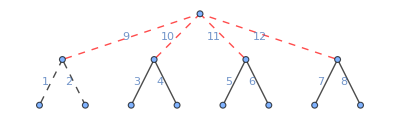
This function takes a topology and an operator with matching number of external bosons and fermions, e.g. the d=11 eight-particle operator {H,H,Lc,Lc,dR,dR,dR,eR}. Notice that the operators have to be sorted so that scalars are first, so {scalar1, scalar2,...., fermion1,fermion2,...}.
Our topologies have the form (see Generate_topologies notebook)
{-Graphics-,{"S","S","F","F","F","F","F","F","NB","NB","NB","NB"},{{1,2,9},{3,4,10},{5,6,11},{7,8,12},{9,10,11,12}}}
where the first entry visualizes the topology and the second entry lists some basic properties of the particles (scalar “S” vs fermion “F” for external particles, new boson “NB” or new fermion “NF” for internal particles). The third entry is the important one, as it encodes the vertices, so {1,2,9} means particles 1, 2, and 9 meet at this vertex (see graph). 

Topology files for most cases of interest are provided by us or can be generated using the Generate_topologies notebook; BNV operators are provided by us, other operators can be readily generated using, for example, Renato Fonseca’s Sym2Int package (https://renatofonseca.net/sym2int).
While not done here, the correct topology file could even be automatically picked according to the number of scalars and fermions in the operator.

We start with the first vertex, {1, 2, 9}, and use it to calculate the representation of particle 9 by multiplying the representations of particles 1 and 2, both H in this example. Since MyReduceRepProduct[{H, H}] provides two solutions for particle 9, {{{0}, {0}, {0, 0}, {2}, 1}, {{0}, {0}, {0, 0}, {0}, 1}}, we generate a new list of lists:
{ {H,H,Lc,Lc,dR,dR,dR,eR, {{0}, {0}, {0, 0}, {2}, 1}}, {H,H,Lc,Lc,dR,dR,dR,eR, {{0}, {0}, {0, 0}, {0}, 1}}}
Then we go on to the second vertex, {3, 4, 10}, and multiply Lc and Lc to obtain the representation for particle 10 and add it to this list of lists, which will eventually look like
{ {H,H,Lc,Lc,dR,dR,dR,eR, rep9, rep10, rep11, rep12}, {H,H,Lc,Lc,dR,dR,dR,eR, different rep9, rep10, rep11, rep12}, ..., {H,H,Lc,Lc,dR,dR,dR,eR, rep9, different rep10, rep11, rep12}, ... }
after we go through all but the last vertex. 
Then we go through all entries in this “particlelist” and check if the last vertex, {9, 10, 11, 12}, contains a singlet, and only keep the solutions that do. 

For diagrams involving multiple Higgs doublets (or multiple anti-Higgs doublets) we need to make sure that vertices don’t vanish, which is the most involved part of this code. Here are the selection rules for vertices involving multiple H: 
any H-H-H-X vertex must have an SU(2)_L  quadruplet X, as doublets give 0;
any H-H-X vertex must have an SU(2)_L  triplet X, as singlets give 0;
at any H-H-X-Y vertex, X*Y must contain an SU(2)_L triplet.
To determine if a vertex has multiple Higgs fields, we read off the positions of all Higgs fields in the operator and then go through the third entry of the topology to see if multiple H ever meet at a vertex. For example, if particle 1 and 2 here are both H (rather than (H,Hc) or (Hc,Hc)), we need to find a vertex with {1,2,X} or {1,2,X,Y} in the vertex list. The functions containsTwoP and containsThreeP check for this.

We check if there are vertices with multiple Higgs bosons and throw away solutions where the vertex vanishes, which in this example is the particle 9 representation {{0}, {0}, {0, 0}, {0}, 1}. In models with multiple Higgs doublets this part of the code could be omitted.
All “particlelist” entries that pass these last checks are possible UV completions for the given diagram, and we output them into the list “viable”.

```mathematica
UVCompletion[topology_,operator_]:=Module[{particlelist,particlelist2,newparticle,viable={},particleset,vertex,Hpositions,HHHXvertices,HHXvertices,HHXYvertices,zeroHHHX,zeroHHX,zeroHHXY,zeroHcHcHcX,zeroHcHcX,zeroHcHcXY,containsTwoP,containsThreeP,ScalarsFirstQ},

(*check if operator is ordered correctly, with scalars at the beginning:*)
ScalarsFirstQ[list_]:=MatchQ[list,{___?(#===H||#===Hc&),___?(#=!=H&&#=!=Hc&)}];
If[!ScalarsFirstQ[operator],Return["Operator needs to be ordered with scalars at the beginning"]];

(*these are the starting particles, we'll be adding the new particles to this list with the following loop*)
particlelist={operator};
(*run over all the vertices in the diagram, except the last one*)
For[vertex=1,vertex<Length[topology[[3]]],vertex++,
particlelist2={};
(*at each vertex {A,B,C,...,Y,Z}, we multiply particles A through Y together to get the representation for Z, then we add Z to the list of particles (if there is more than one solution, each solution gets its own list {SM1, SM2, SM3,...Z})*)
For[particleset=1,particleset<=Length[particlelist],particleset++,
newparticle=MyReduceRepProduct[Table[particlelist[[particleset]][[topology[[3,vertex,i]]]],{i,1,Length[topology[[3,vertex]]]-1}]];
Table[AppendTo[particlelist2,Join[particlelist[[particleset]],{newparticle[[k]]}]],{k,Length[newparticle]}];
];
particlelist=particlelist2;
(*now particlelist is a list of lists; each entry is a set of viable quantum numbers up to some vertex, then it runs through again until the second-to-last vertex*)
];
(*now we go through each list in particlelist and see if the last vertex is a singlet; if yes, we add all the new particles to the list 'viable'. Also check if vertices with multiple Higgses vanish, and discard those solutions. Can easily add SM particles or topology or operator to this list for a more elaborate output*)
For[particleset=1,particleset<=Length[particlelist],particleset++,
If[ContainsSinglet[Table[particlelist[[particleset]][[Last[topology[[3]]][[i]]]],{i,1,Length[Last[topology[[3]]]]}]] (*check last vertex*),
(*the rest goes through vertices with two or three H or Hc and makes sure the vertices are not zero:*)

(*Define a function to check if a vertex  contains two or three particles. E.g. containsTwoP[{1,2,9},{1,2}] = True but containsTwoP[{3,4,10},{1,2}] = False*)
containsTwoP[sublist_,numbers_]:=Length[Intersection[sublist,numbers]]==2;
containsThreeP[sublist_,numbers_]:=Length[Intersection[sublist,numbers]]==3;

Hpositions=Flatten[Position[operator,H]];
HHHXvertices=Select[topology[[3]],containsThreeP[#,Hpositions]&];
HHXvertices=Select[topology[[3]],containsTwoP[#,Hpositions]&&Length[#]==3&];
HHXYvertices=Select[topology[[3]],containsTwoP[#,Hpositions]&&Length[#]==4&];
(*check if the X in any HHHX vertex is a doublet (so HHHX vanishes); zeroHHHX==True in that case:*)
zeroHHHX=MemberQ[Table[particlelist[[particleset]][[Complement[HHHXvertices[[threeHvertex]],Hpositions][[1]]]][[4,1]]==1,{threeHvertex,Length[HHHXvertices]}],True];
(*check if the X in any HHX vertex is a singlet (so HHX vanishes); zeroHHX==True in that case:*)
zeroHHX=MemberQ[Table[particlelist[[particleset]][[Complement[HHXvertices[[twoHvertex]],Hpositions][[1]]]][[4,1]]==0,{twoHvertex,Length[HHXvertices]}],True];
(*check if the XY rep product in any HHXY vertex contains a triplet (so HHXY does not vanish); zeroHHXY==True otherwise:*)
zeroHHXY=MemberQ[Table[MemberQ[MyReduceRepProduct[{particlelist[[particleset]][[Complement[HHXYvertices[[twoHvertex]],Hpositions][[1]]]],particlelist[[particleset]][[Complement[HHXYvertices[[twoHvertex]],Hpositions][[2]]]]}][[All,4]],{2}],{twoHvertex,Length[HHXYvertices]}],False];
(*repeat for Hc; no need to change anything because everything comes from SU(2)L part*)
Hpositions=Flatten[Position[operator,Hc]];
HHHXvertices=Select[topology[[3]],containsThreeP[#,Hpositions]&];
HHXvertices=Select[topology[[3]],containsTwoP[#,Hpositions]&&Length[#]==3&];
HHXYvertices=Select[topology[[3]],containsTwoP[#,Hpositions]&&Length[#]==4&];
(*check if the X in any HHHX vertex is a doublet (so HHHX vanishes); zeroHHHX==True in that case:*)
zeroHcHcHcX=MemberQ[Table[particlelist[[particleset]][[Complement[HHHXvertices[[threeHvertex]],Hpositions][[1]]]][[4,1]]==1,{threeHvertex,Length[HHHXvertices]}],True];
(*check if the X in any HHX vertex is a singlet (so HHX vanishes); zeroHHX==True in that case:*)
zeroHcHcX=MemberQ[Table[particlelist[[particleset]][[Complement[HHXvertices[[twoHvertex]],Hpositions][[1]]]][[4,1]]==0,{twoHvertex,Length[HHXvertices]}],True];
(*check if the XY rep product in any HHXY vertex contains a triplet (so HHXY does not vanish); zeroHHXY==True otherwise:*)
zeroHcHcXY=MemberQ[Table[MemberQ[MyReduceRepProduct[{particlelist[[particleset]][[Complement[HHXYvertices[[twoHvertex]],Hpositions][[1]]]],particlelist[[particleset]][[Complement[HHXYvertices[[twoHvertex]],Hpositions][[2]]]]}][[All,4]],{2}],{twoHvertex,Length[HHXYvertices]}],False];
(*if all vertices are non-zero, add them to viable:*)
If[zeroHHHX==False&&zeroHHX==False&&zeroHHXY==False&&zeroHcHcHcX==False&&zeroHcHcX==False&&zeroHcHcXY==False,
(*also add the topology to viable to provide the complete Feynman diagram; replace the external particle names by their SM names*)
AppendTo[viable,{topology,Join[
Table[particlelist[[particleset]][[par]]/.ReplaceSMnames,{par,1,Count[topology[[2]],"S"]+Count[topology[[2]],"F"]}],(*external particles, match back to SM names*)
Table[particlelist[[particleset]][[par]],{par,Count[topology[[2]],"S"]+Count[topology[[2]],"F"]+1,Length[topology[[2]]]}]]}](*internal particles*)
];
];
];
Return[viable]
]
```

Notice that all internal fermions are assumed to be massive Dirac particles, so both chiralities are present in the model. Each fermion line comes with a chirality flip, as it should for non-derivative operators, and the chirality returned by UVCompletion is the one flowing into the second vertex. The fermion has the opposite chirality when it is emitted at the first vertex.

In this example, there is only one UV completion with new particles of spin ≤ 1, all scalars here:

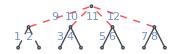
```mathematica
topo={-Graphics-,{"S","S","F","F","F","F","F","F","NB","NB","NB","NB"},{{1,2,9},{3,4,10},{5,6,11},{7,8,12},{9,10,11,12}}};
oper={H,H,Lc,Lc,dR,dR,dR,eR};(*operator, i.e. external particles. Order matters, scalars need to be at the beginning of the list*)
UVCompletion[topo,oper]
```

{{{-Graphics-,{S,S,F,F,F,F,F,F,NB,NB,NB,NB},{{1,2,9},{3,4,10},{5,6,11},{7,8,12},{9,10,11,12}}},{H,H,Lc,Lc,dR,dR,dR,eR,{{0},{0},{0,0},{2},1},{{0},{0},{0,0},{2},1},{{0},{0},{0,1},{0},-2/3},{{0},{0},{1,0},{0},-4/3}}}}

So particle 9 in the diagram is a scalar with gauge representation {{0, 0}, {2}, 1} (color singlet, SU(2)L triplet, with hypercharge 1), 
particle 10 has the same quantum numbers as 9 (although we implicitly treat it as a separate particle, otherwise we’d have to make sure vertices involving 9 and 10 don’t vanish due to symmetry, in analogy to the Higgs case), particle 11 is a scalar with gauge representation {{0,1}, {0}, -2/3} (3-bar under color SU(3), SU(2)L singlet, with hypercharge -2/3), and particle 12 is a color triplet with hypercharge -4/3.

In other cases, we obtain multiple solutions; UVCompletion[...] is always a list of valid new-particle representations:

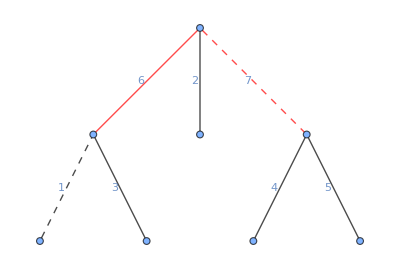
```mathematica
topo={-Graphics-,{"S","F","F","F","F","NF","NB"},{{1,3,6},{2,6,7},{4,5,7}}};
oper={Hc,dR,Q,Q,Lc};(*operator, i.e. external particles. Order matters, scalars need to be at the beginning of the list*)
UVCompletion[topo,oper]
```

{{{-Graphics-,{S,F,F,F,F,NF,NB},{{1,3,6},{2,6,7},{4,5,7}}},{Hc,dR,Q,Q,Lc,{{1},{0},{1,0},{2},-1/3},{{1},{1},{0,1},{2},-2/3}}},{{-Graphics-,{S,F,F,F,F,NF,NB},{{1,3,6},{2,6,7},{4,5,7}}},{Hc,dR,Q,Q,Lc,{{1},{0},{1,0},{0},-1/3},{{1},{1},{0,1},{0},-2/3}}}}

Now that we can obtain UV completions for a given diagram, we just need consider all possible permutations of external fields. The function MyPermutations[operator] automatically generates all permutations while keeping scalars at the beginning of the list.
Example: UV completions for one d=6 BNV SMEFT operator:

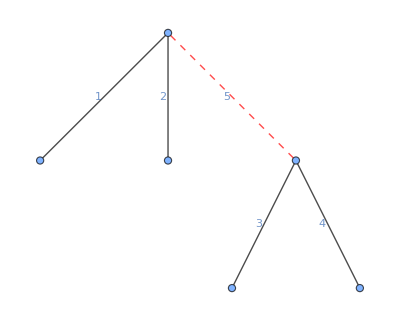
```mathematica
topo={-Graphics-,{"F","F","F","F","NB"},{{1,2,5},{3,4,5}}};
oper={Q,Q,Q,L};
(*perform external particle permutations here:*)
operatorpermutations=MyPermutations[oper];(* = {{"Q","Q","Q","L"},{"Q","Q","L","Q"},{"Q","L","Q","Q"},{"L","Q","Q","Q"}}*)
fulllist={};
For[perm=1,perm<=Length[operatorpermutations],perm++,
fulllist=Join[fulllist,UVCompletion[topo,operatorpermutations[[perm]]]];
];
fulllist
```

{{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,Q,L,{{0},{0},{0,1},{2},1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,Q,L,{{0},{0},{0,1},{0},1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,L,Q,{{0},{0},{0,1},{2},1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,L,Q,{{0},{0},{0,1},{0},1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,L,Q,Q,{{0},{0},{1,0},{2},-1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,L,Q,Q,{{0},{0},{1,0},{0},-1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{L,Q,Q,Q,{{0},{0},{1,0},{2},-1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{L,Q,Q,Q,{{0},{0},{1,0},{0},-1/3}}}}

The list is redundant in the sense that  {"Q","Q","Q","L",{{0},{0},{0,1},{2},1/3}} and  {"Q","L","Q","Q",{{0},{0},{1,0},{2},-1/3}} are actually the same solution, just with a different momentum routing on the internal line. Also, exchanging particles 1 and 2 or 3 and 4 obviously give the same representation for particle 5, but show up as different entries above. The next step is then to remove equivalent UV completions.

## Equivalence of UV completions

To determine if two UV completions are equivalent, we turn our Feynman diagram into a directed graph via the function MomentumGraph (see Generate_topologies notebook) to incorporate the information about momentum flow. Then, we change all internal anti-particles (as determined by our RepNaming function) to particles and flip the momentum arrow via the function FullParticleDiagram, which generates a canonical graph. This requires several functions from Generate_topologies:

```mathematica
MakeDirectedGraph[g_Graph] :=Graph[DirectedEdge@@@EdgeList[g],{EdgeLabels->(EdgeLabels/. Options[g,EdgeLabels])/. Rule[UndirectedEdge[a_,b_],val_]:>Rule[DirectedEdge[a,b],val],EdgeStyle->(EdgeStyle/. Options[g,EdgeStyle])/. Rule[UndirectedEdge[a_,b_],val_]:>Rule[DirectedEdge[a,b],val]}]



FlipEdgeByLabel[g_Graph,labelText_]:=Module[{edges,labelsRaw,stylesRaw,labelsList,stylesList,targetPairs,keys,revKeys,mapping,newEdges,newLabels,newStyles,otherOpts,extractText,canon},(*helper:extract visible text from label objects*)
extractText[Placed[Style[Text[x_,___],___],___]]:=x;
extractText[Placed[Text[x_,___],___]]:=x;
extractText[Text[x_,___]]:=x;
extractText[x_]:=x;
(*canonicalize label for matching (so 5 and "5" compare equal)*)canon[x_]:=If[StringQ[x],x,ToString[x,InputForm]];
(*1) get edge list and existing label/style rules (safe defaults)*)edges=EdgeList[g];
labelsRaw=EdgeLabels/. Options[g]/. EdgeLabels->{};
stylesRaw=EdgeStyle/. Options[g]/. EdgeStyle->{};
(*ensure we have lists of rules (not Associations)*)labelsList=If[MatchQ[labelsRaw,_Rule|_RuleDelayed],{labelsRaw},labelsRaw];
stylesList=If[MatchQ[stylesRaw,_Rule|_RuleDelayed],{stylesRaw},stylesRaw];
(*3) find label rule(s) whose visible text matches (robust to 5 vs "5")*)targetPairs=Select[labelsList,canon[extractText[#[[2]]]]===canon[labelText]&];
(*nothing found->return original graph unchanged*)If[targetPairs==={},Return[g]];
(*4) build mapping oldEdge->reversedEdge (handle Directed/Undirected)*)keys=targetPairs[[All,1]];
revKeys=keys/. {DirectedEdge[a_,b_]:>DirectedEdge[b,a],UndirectedEdge[a_,b_]:>UndirectedEdge[b,a]};
mapping=Thread[keys->revKeys];
(*5) apply mapping to edges and rule keys using Replace (/.),not ReplacePart*)newEdges=Replace[edges,mapping,{1}];
newLabels=labelsList/. mapping;
newStyles=stylesList/. mapping;
(*6) preserve other options and rebuild graph*)otherOpts=DeleteCases[Options[g],(EdgeLabels->_)|(EdgeStyle->_)];
Graph[newEdges,Sequence@@otherOpts,EdgeLabels->newLabels,EdgeStyle->newStyles]]


FixEdgeDirections[g0_Graph,clusters_List]:=Module[{newg=g0,extractText,canon,verts,labelsRaw,labels,vertexLabelSets,uniqueLabels,posIndices,i,j,clLeftCanon,clRightCanon,vFrom,vTo,edgeRule,srcdst,flipped={},lab,ReturnFlipped=False,labelsFromGraph,clCanon,vHub},(*---helpers---*)extractText[Placed[Text[x_,___],___]]:=x;
extractText[Text[x_,___]]:=x;
extractText[x_]:=x;
(*canonicalize so 7 and "7" compare equal*)canon[x_]:=If[StringQ[x],x,ToString[x]];
(*build a fresh labels map from the current graph*)labelsFromGraph[gg_]:=Module[{lr=EdgeLabels/. Options[gg]/. EdgeLabels->{}},lr/. (Rule|RuleDelayed)[UndirectedEdge[a_,b_],v_]:>Rule[DirectedEdge[a,b],v]];
(*---prepare vertex incident-label sets (order-independent,canonicalized)---*)labels=labelsFromGraph[newg];
verts=VertexList[newg];
vertexLabelSets=AssociationThread[verts,Table[Sort[DeleteDuplicates[canon/@(extractText/@Cases[Normal[labels],Rule[DirectedEdge[a_,b_],val_]/;(a===v||b===v):>val])]],{v,verts}]];
(*unique labels appearing somewhere in clusters*)uniqueLabels=DeleteDuplicates[Flatten[clusters]];
(*iterate over each label occurring in clusters*)Do[lab=uniqueLabels[[k]];
posIndices=Flatten[Table[If[MemberQ[clusters[[t]],lab],t,Nothing],{t,Length[clusters]}]];
If[Length[posIndices]<1,Continue[]];
labels=labelsFromGraph[newg];
edgeRule=FirstCase[Normal[labels],Rule[e_,val_]/;canon[extractText[val]]===canon[lab]:>e,Missing["NoSuchLabel"]];
If[edgeRule===Missing["NoSuchLabel"],Continue[]];
srcdst=List@@edgeRule;
If[Length[posIndices]===1,(*Leaf/external:always point toward the hub*)clCanon=Sort[canon/@clusters[[posIndices[[1]]]]];
vHub=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clCanon:>v,Missing["NoHub"]];
If[vHub===Missing["NoHub"],Continue[]];
If[srcdst[[2]]=!=vHub,newg=FlipEdgeByLabel[newg,lab];AppendTo[flipped,lab]],(*Internal:point from earlier cluster hub to later cluster hub*)i=Min[posIndices];j=Max[posIndices];
clLeftCanon=Sort[canon/@clusters[[i]]];
clRightCanon=Sort[canon/@clusters[[j]]];
vFrom=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clLeftCanon:>v,Missing["NoHub"]];
vTo=FirstCase[Keys[vertexLabelSets],v_/;vertexLabelSets[v]===clRightCanon:>v,Missing["NoHub"]];
If[vFrom===Missing["NoHub"]||vTo===Missing["NoHub"],Continue[]];
If[srcdst[[1]]=!=vFrom,newg=FlipEdgeByLabel[newg,lab];AppendTo[flipped,lab]]],{k,Length[uniqueLabels]}];
If[ReturnFlipped,{newg,flipped},newg]]

(*function that takes a graph and a edge label and removes the direction of the edge*)
MakeEdgeUndirectedByLabel[g_Graph,lbl_]:=Module[{labelsOpt,labelsRules,edgeToChange,undirectedEdge,newEdges,opts,newOpts,labelMatchQ},(*get current EdgeLabels rules*)labelsOpt=AbsoluteOptions[g,EdgeLabels];
labelsRules=If[labelsOpt==={},{},EdgeLabels/. First[labelsOpt]];
(*robust matcher:handles Text["1"],Text[1],numeric 1,etc.*)labelMatchQ[rhs_]:=AnyTrue[Cases[rhs,Text[t_,___]:>t,∞],Function[t,t===lbl||ToString[t]===ToString[lbl]]];
(*find the directed edge with the given label*)edgeToChange=FirstCase[labelsRules,(e_->rhs_)/;labelMatchQ[rhs]:>e,Missing[]];
If[edgeToChange===Missing[],Return[g]];
undirectedEdge=UndirectedEdge@@List@@edgeToChange;
newEdges=EdgeList[g]/. edgeToChange->undirectedEdge;
opts=Options[g];
newOpts=opts/. edgeToChange->undirectedEdge;
Graph[VertexList[g],newEdges,Sequence@@newOpts]]

(*takes a topology and spits out the vertex structure, e.g. {{"F","F","NB"},{"F","NF","S"},{"F","NF","S"},{"NB","NB","S"},{"NB","NF","NF"}}*)
VertexStructure[{graph_,first_List,second_List}]:=Module[{mapped},mapped=second/. i_Integer:>first[[i]];
Sort[Sort/@mapped]]

(*This function constructs a directed graph out of a given UV completion so that all internal lines are particles rather than antiparticles (as determined by RepNaming), flipping arrows as needed. For self-conjugate particles, the arrow is removed. Notice that we drop chirality information here.*)
FullParticleDiagram[UVComp_]:=Module[{graph,particles,med,DropChirality},

DropChirality[expr_]:=expr /. {(*Scalar (S):{0},{0}*){{0}, {0}, rest___} :> {"S",rest},(*Fermion (F):{0},{1} or {1},{0}*){{0}, {1},rest___} :> {"F", rest},{{1}, {0}, rest___} :> {"F",rest},(*Vector (V):{1},{1}*){{1}, {1}, rest___} :> {"V", rest}};

(*basically MomentumGraph from Generate_topologies:*);
graph=FixEdgeDirections[MakeDirectedGraph[UVComp[[1,1]]],UVComp[[1]][[3]]];
particles=DropChirality[UVComp[[2]]];
For[med=1+Count[UVComp[[1,2]],"S"|"F"],med<=Length[particles],med++,
Which[particles[[med]]!=RepNaming[particles[[med]]],
graph=FlipEdgeByLabel[graph,med];
particles[[med]]=RepNaming[particles[[med]]];,
ConjugateRep[particles[[med]]]==particles[[med]],
graph=MakeEdgeUndirectedByLabel[graph,med];,
True, ];
];
Return[ToExpression[StringReplace[ToString[InputForm[graph]],"\""~~x:DigitCharacter..~~"\"":>ToString[particles[[ToExpression[x]]],InputForm]]]];
];
```

Let’s try this out on our d=6 example, resulting in 8 directed graphs with re-ordered momentum flow so that the internal particle is always a particle, i.e. with unbarred SU(3) representation:

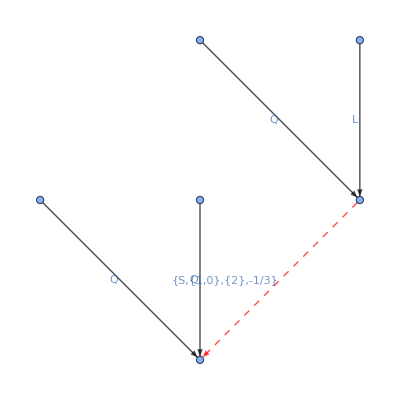
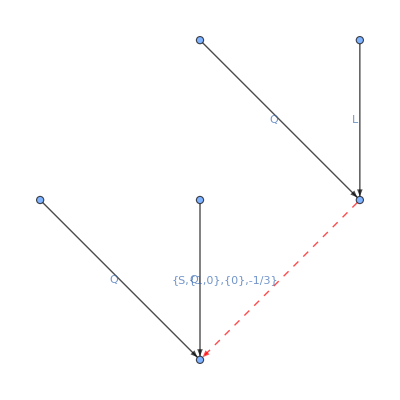
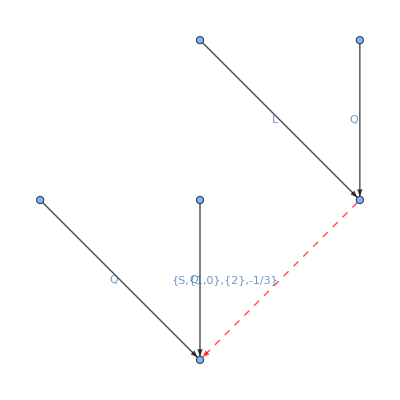
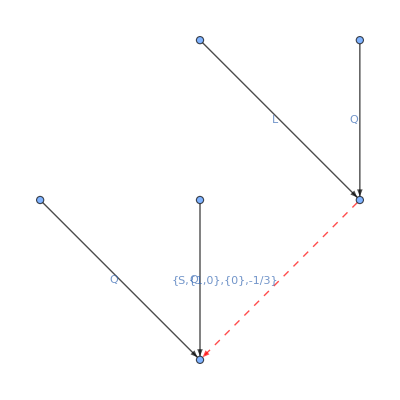
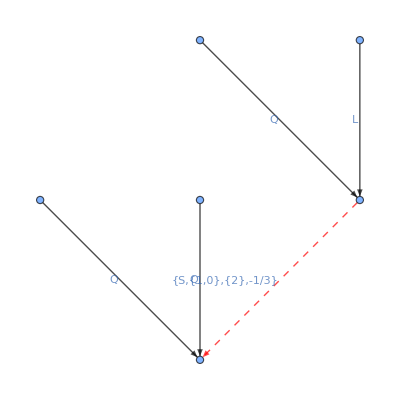
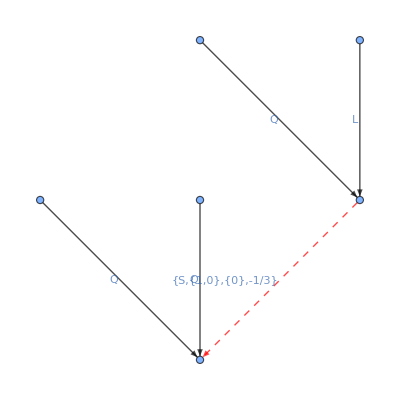
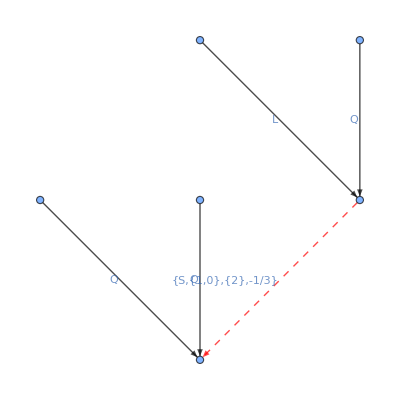
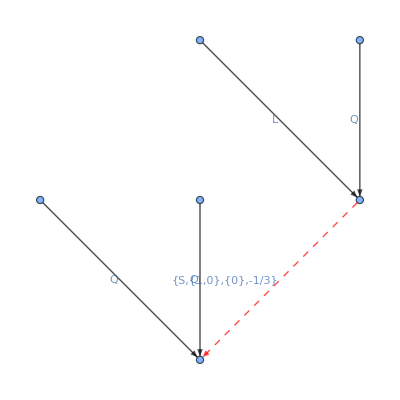

```mathematica
Table[FullParticleDiagram[fulllist[[j]]],{j,Length[fulllist]}]
```

Notice that self-conjugate bosons would have no arrow on their lines at all since we are actually tracking charge flow rather than momentum.
Terrible label placement aside, we can see by eye that there are only two different diagrams. To check this, we convert the edge labels into colors (so all Q lines get one color, all L lines get one color, all {{0},{0},{0,1},{0},1/3} lines get one color,...) and then use IGraph/M to check if those colored directed graphs are isomorphic via the function CompareUVCompletionsQ[uv1,uv2]. This function first checks if uv1 and uv2 have the same topologies, external particles, and internal particles (after converting them all to particles), and only then compares the colored directed diagrams.

Need IGraph/M for graph isomorphism, just run this installer to download the package:

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

Load IGraph/M:

```mathematica
Needs["IGraphM`"];
ParallelNeeds["IGraphM`"];
```

```mathematica
CompareUVCompletionsQ[UVComp1_,UVComp2_]:=Module[
{graph1,graph2,edgeLabels1,edgeLabels2,uniqueLabels,colorIndexAssoc,edgeColorAssoc1,edgeColorAssoc2,extPar1,extPar2,mediators1,mediators2,DropChirality},
(*Topologies; only checking vertex structure, i.e. same {{"F","F","NB"},{"F","NF","S"},...} to make it insensitive to particle numbering*)
If[!(VertexStructure[UVComp1[[1]]]===VertexStructure[UVComp2[[1]]]),Return[False]];
(*Operators*)
extPar1=TakeWhile[UVComp1[[2]],StringQ];
extPar2=TakeWhile[UVComp2[[2]],StringQ];
If[!(Sort[extPar1]===Sort[extPar2]),Return[False]];
(*Mediators, dropping chirality:*)
DropChirality[expr_]:=expr /. {(*Scalar (S):{0},{0}*){{0}, {0}, rest___} :> {"S",rest},(*Fermion (F):{0},{1} or {1},{0}*){{0}, {1},rest___} :> {"F", rest},{{1}, {0}, rest___} :> {"F",rest},(*Vector (V):{1},{1}*){{1}, {1}, rest___} :> {"V", rest}};
mediators1=Map[RepNaming,DropChirality[UVComp1[[2]][[Length[extPar1]+1;;]]]];
mediators2=Map[RepNaming,DropChirality[UVComp2[[2]][[Length[extPar2]+1;;]]]];
If[!(Sort[mediators1]===Sort[mediators2]),Return[False]];
(*do full graph comparison*);
graph1=DirectedGraph[FullParticleDiagram[UVComp1]];
graph2=DirectedGraph[FullParticleDiagram[UVComp2]];
edgeLabels1=Cases[EdgeLabels/. AbsoluteOptions[graph1,EdgeLabels],Rule[e_,Placed[Text[label_,___],___]]:>(e->label)];
(*sometimes we use Placed[Style[Text[..]]] in our graphs instead of Placed[Text[..]], make sure we catch that:*);
If[edgeLabels1=={},
edgeLabels1=Cases[EdgeLabels/. AbsoluteOptions[graph1,EdgeLabels],Rule[e_,Placed[Style[Text[label_,___],___],___]]:>(e->label)];
edgeLabels2=Cases[EdgeLabels/. AbsoluteOptions[graph2,EdgeLabels],Rule[e_,Placed[Style[Text[label_,___],___],___]]:>(e->label)];,
edgeLabels2=Cases[EdgeLabels/. AbsoluteOptions[graph2,EdgeLabels],Rule[e_,Placed[Text[label_,___],___]]:>(e->label)];
];
uniqueLabels=DeleteDuplicates[Join[edgeLabels1,edgeLabels2][[All,2]]];
colorIndexAssoc=AssociationThread[uniqueLabels->Range[Length[uniqueLabels]]];
edgeColorAssoc1=Association[edgeLabels1/. (e_->label_):>(e->colorIndexAssoc[label])];
edgeColorAssoc2=Association[edgeLabels2/. (e_->label_):>(e->colorIndexAssoc[label])];
If[Normal[edgeColorAssoc1]=={}||Normal[edgeColorAssoc2]=={},Print["something is wrong"];];
(*now we have two directed graphs with colored edges, use IGraph/M's IGVF2IsomorphicQ to check their isomorphism:*);
Return[IGVF2IsomorphicQ[{graph1,"EdgeColors"->edgeColorAssoc1},{graph2,"EdgeColors"->edgeColorAssoc2}]];
]
```

Now we can automatically check if two UV completions are equivalent,

```mathematica
CompareUVCompletionsQ[{{-Graphics-,{"F","F","F","F","NB"},{{1,2,5},{3,4,5}}},{"Q","Q","Q","L",{{0},{0},{0,1},{2},1/3}}},{{-Graphics-,{"F","F","F","F","NB"},{{1,2,5},{3,4,5}}},{"L","Q","Q","Q",{{0},{0},{1,0},{2},-1/3}}}]
```

True

and we can use this function to delete duplicates from our UV completion list:

```mathematica
DeleteDuplicates[fulllist,CompareUVCompletionsQ[#1,#2]&]
```

{{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,Q,L,{{0},{0},{0,1},{2},1/3}}},{{-Graphics-,{F,F,F,F,NB},{{1,2,5},{3,4,5}}},{Q,Q,Q,L,{{0},{0},{0,1},{0},1/3}}}}

Indeed, there are only two inequivalent UV completions for this QQQL operator, in agreement with previous results: nothing but the scalar leptoquarks S_3 and S_1:

```mathematica
RepName[{SU3,SU2,U1},#]&/@{{{0,1},{2},1/3},{{0,1},{0},1/3}}
```

{OverBar[3]⊗3⊗1/3,OverBar[3]⊗1⊗1/3}

A more complicated example of a d=9 operator, where CompareUVCompletionsQ reduces the number of UV completions from 72 to 22:

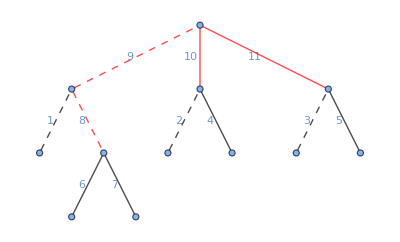
```mathematica
topo={-Graphics-,{"S","S","S","F","F","F","F","NB","NB","NF","NF"},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}};
oper={Hc,Hc,H,ec,Q,dR,dR};
(*perform external particle permutations here:*)
operatorpermutations=MyPermutations[oper];
fulllist={};
For[perm=1,perm<=Length[operatorpermutations],perm++,
fulllist=Join[fulllist,UVCompletion[topo,operatorpermutations[[perm]]]];
];
fulllist//Length
fulllistNoDuplicates=DeleteDuplicates[fulllist,CompareUVCompletionsQ[#1,#2]&];
fulllistNoDuplicates//Length
Print["Random UV example:"];
RandomChoice[fulllistNoDuplicates]
```

72

22

Random UV example:

{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{Hc,Hc,H,Q,ec,dR,dR,{{0},{0},{0,1},{0},-2/3},{{0},{0},{0,1},{1},-7/6},{{1},{0},{1,0},{2},-1/3},{{1},{0},{0,0},{1},3/2}}}

Notice that our CompareUVCompletionsQ function is not very fast, which might become an issue when looking at UV completions of d >> 6 operators. Instead of working with graphs and IGraph/M, one can instead use the vertex list of the topology, say {{6, 7, 8}, {1, 8, 9}, {2, 4, 10}, {3, 5, 11}, {9, 10, 11}}, to read off charge flow and define a canonical expression, allowing for a much faster use of DeleteDuplicatesBy instead of DeleteDuplicates. Please contact the authors if that significantly faster code is desired.

UVCompletion[...] (ran through CompareUVCompletionsQ) now gives us a list of UV completions for a given topology and operator. By construction, these Feynman diagrams have non-zero vertices and hence give non-zero amplitudes. This does NOT mean, unfortunately, that the resulting amplitude can be approximated by the non-derivative operator we started out with. To integrate out the heavy internal particles at leading order simply corresponds to replacing the internal operators by 1/M^2 for bosons and 1/M for fermions. In the resulting amplitude, all external particles are evaluated at the same point, and are hence subject to the usual symmetrization and anti-symmetrization rules. This is less important for fermions, because they come in three distinct generations, but crucial for the external Higgs particles, as they come in only one generation. Whenever we UV complete operators with two or more H (or two or more anti-H), we need to make sure that the resulting amplitude does not vanish in the constant-propagator limit due to symmetries, e.g. because it comes out as anti-symmetric under H exchange. The next step is then to check UV completions of multi-Higgs operators and filter out the UV completions that give a vanishing amplitude in the constant-propagator limit (which end up giving non-vanishing derivative operators).

## Checking for Higgs asymmetry

This function takes a UV completion, “integrates out” the internal particles using a constant propagator by properly contracting the vertex invariants of the diagram, and then checks the resulting amplitude for asymmetry in any pair of Higgs fields or anti-Higgs fields:

```mathematica
AsymmetricHiggsQ[uvcompletion_]:=Module[{topology,vertex,vertexfactors={},newparticlelabels,newparticlelabelsbar,newparticlestates,newparticlestatesbar,vertexproduct,Hlabels,Hclabels,totalantisymlist={},SMparticlestates,w,inv,k,in,confirmedNonZero,trial,failed,symbolicCheck},
(*identify the particle label/name of the Higgses and anti-Higgses*)
Hlabels=ToExpression[StringJoin["p",IntegerString[#]]&/@Flatten[Position[uvcompletion[[2]],"H"]]];
Hclabels=ToExpression[StringJoin["p",IntegerString[#]]&/@Flatten[Position[uvcompletion[[2]],"Hc"]]];
(*If there are less than 2 H or 2 Hc, no need to check for antisymmetry, return False*)
If[Length[Hlabels]<2&&Length[Hclabels]<2,Return[False];];
(*if there are multiple Higgses, need to calculate asymmetry:*)
topology=uvcompletion[[1]];
(*figure out which of the particles are internal and need to be integrated out. we get the labels of all new particles from topology, so {p3,p5,...}*)
newparticlelabels=ToExpression[StringJoin["p",IntegerString[#]]&/@Flatten[Join[Position[topology[[2]],"NB"],Position[topology[[2]],"NF"]]]];
(*and we also get p3bar, p5bar to distinguish incoming and outgoing internal particles:*);
newparticlelabelsbar=ToExpression[StringJoin["p",IntegerString[#],"bar"]&/@Flatten[Join[Position[topology[[2]],"NB"],Position[topology[[2]],"NF"]]]];
(*run over all the vertices in the diagram, except the last one, and calculate the full group invariants at each vertex, renaming the multiplets by particle labels p1, p2, p3 etc that match the labelling in the topology. We treat all but the last particle in each vertex as incoming, and the last one as outgoing (Conjugations -> True), following the same logic as in UVCompletions. We distinguish 3 and 4-particle vertices:*)
For[vertex=1,vertex<Length[topology[[3]]],vertex++,
If[Length[topology[[3]][[vertex]]]==3,
(*3-particle vertex*)
inv=Invariants[group,{uvcompletion[[2]][[topology[[3,vertex,1]]]],uvcompletion[[2]][[topology[[3,vertex,2]]]],uvcompletion[[2]][[topology[[3,vertex,3]]]]}/.InverseReplaceSMnames,{Conjugations->{False,False,True}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]<>"bar"]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ", topology[[3]][[vertex]]]];
If[vertex==1,
(*for first vertex, vertexfactors = Invariants[...]*)
vertexfactors=inv;,
(*for all subsequent vertices, vertexfactors is updated to a nested list: {{inv(vertex1)[1],inv(vertex2)[1],...},{inv(vertex1)[2],inv(vertex2)[1],...} so that vertexfactors[[1]] collects one possible set of diagram invariants, vertexfactors[[2]] another, etc. *)
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];,
(*4-particle vertex*)
inv=Invariants[group,{uvcompletion[[2]][[topology[[3,vertex,1]]]],uvcompletion[[2]][[topology[[3,vertex,2]]]],uvcompletion[[2]][[topology[[3,vertex,3]]]],uvcompletion[[2]][[topology[[3,vertex,4]]]]}/.InverseReplaceSMnames,{Conjugations->{False,False,False,True}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]],d->ToExpression[ToString[p]<>ToString[topology[[3,vertex,4]]]<>"bar"]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];
If[vertex==1,
(*for first vertex, vertexfactors = Invariants[...]*)
vertexfactors=inv;,
(*for all subsequent vertices, vertexfactors is updated to a nested list: {{inv(vertex1)[1],inv(vertex2)[1],...},{inv(vertex1)[2],inv(vertex2)[1],...} so that vertexfactors[[1]] collects one possible set of diagram invariants, vertexfactors[[2]] another, etc. *)
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];
];
];
(*At the last vertex, all particles are incoming, otherwise same procedure, the group invariants for each vertex are added to the list vertexfactors:*)
vertex=Length[topology[[3]]];
If[Length[topology[[3]][[vertex]]]==3,
(*3-particle vertex*)
inv=Invariants[group,{uvcompletion[[2]][[topology[[3,vertex,1]]]],uvcompletion[[2]][[topology[[3,vertex,2]]]],uvcompletion[[2]][[topology[[3,vertex,3]]]]}/.InverseReplaceSMnames,{Conjugations->{False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];
(*thread it into the non-empty vertexfactor list*);
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];,
(*4-particle vertex*)
inv=Invariants[group,{uvcompletion[[2]][[topology[[3,vertex,1]]]],uvcompletion[[2]][[topology[[3,vertex,2]]]],uvcompletion[[2]][[topology[[3,vertex,3]]]],uvcompletion[[2]][[topology[[3,vertex,4]]]]}/.InverseReplaceSMnames,{Conjugations->{False,False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]],d->ToExpression[ToString[p]<>ToString[topology[[3,vertex,4]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ", topology[[3]][[vertex]]]];
(*thread it into the non-empty vertexfactor list*);
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];
(*for each internal particle, say p3, we now read off all multiplet components from their occurance in vertexfactors, so this gives all spin and gauge multiplet states of p3, and then same for p3bar*);
newparticlestates=Values[GroupBy[DeleteDuplicates[Cases[vertexfactors,Alternatives@@(#[___]&/@newparticlelabels),All]],Head]];
newparticlestatesbar=newparticlestates/.Thread[newparticlelabels -> newparticlelabelsbar];
(*the most important part: we multiply all vertex factors, which is similar to the diagram amplitude since propagators are constants in our non-derivative ansatz:*);
For[in=1,in<=Length[vertexfactors],in++,
vertexproduct=Apply[Times,vertexfactors[[in]]];
(*in this amplitude, each new-particle state shows up once as p3[...] and once as p3bar[...]. The propagator connects these two if they have the same argument. So, integrating out p3 boils down to taking the derivative of the amplitude with respect to p3[x] and p3bar[x], and sum over x. Then we do the same for all other new particles:*);
For[w=1,w<=Length[newparticlestates],w++,
vertexproduct=Sum[D[vertexproduct,newparticlestates[[w]][[i]],newparticlestatesbar[[w]][[i]]],{i,Length[newparticlestates[[w]]]}]
];
(*the final vertexproduct only depends on the external SM states, i.e. the internal particles have been integrated out, properly taking care of the group contractions.*)
(*now identify the external SM states: p1[..], p2[...], used later to plug in numbers for these 'wavefunctions'*);
SMparticlestates=DeleteDuplicates[Cases[vertexproduct,Alternatives@@(#[___]&/@ToExpression[StringJoin["p",IntegerString[#]]&/@Range[Length[topology[[2]]]]]),All]];
(*now we take our final vertexproduct and set all the H labels equal to each other and all Hc labels equal to each other. If the 'amplitude' is antisymmetric under H <-> H exchange or Hc <-> Hc exchange it'll give 0, otherwise non-zero.*)
AppendTo[totalantisymlist,vertexproduct/.If[Length[Hlabels]>1,Thread[Rest[Hlabels]->First[Hlabels]],{}]/.If[Length[Hclabels]>1,Thread[Rest[Hclabels]->First[Hclabels]],{}]];
];
(*totalantisymlist is a list,each entry a possible way to have an invariant diagram.A zero entry means that choice is antisymmetric under H or Hc exchange,so will not lead to a non-derivative operator.If there is at least one non-zero entry in this list,the UV completion is fine and gives a non-derivative operator.Since the expression can become quite large,trying to simplify this expression to figure out if it is 0 can take a lot of time.Instead,we throw in random rational numbers for all the external-state wavefunctions p1[..],p2[..] etc,which gives 0 if the Higgses are antisymmetrized but some non-zero value otherwise.Much quicker and reliable enough,odds are slim that we would get an accidental cancellation.Just in case, run it up to five times, stopping as soon as we find a confirmed non-zero entry. only if we get 0 for five different numerical tries do we check if the expression is 0 for all SMparticlestates*)confirmedNonZero=False;failed=False;
Do[
trial=totalantisymlist/. Thread[SMparticlestates->Table[(-1)^RandomInteger[{0,1}] RandomInteger[{1,1000}]/RandomInteger[{1,1000}],{Length[SMparticlestates]}]];
(*make sure we're looking at numbers,i.e.everything was properly substituted*)
If[!AllTrue[trial,NumericQ],Print["trial aren't numbers!"];failed=True;Break[];];
(*check if these numerical expressions are zero or not;AnyTrue short-circuits as soon as one entry is confirmed non-zero, in which case we return False, as the amplitude is non-zero*)
If[AnyTrue[trial,!PossibleZeroQ[#,Method->"ExactAlgebraics"]&],confirmedNonZero=True;Break[];
],
{5}];

(*A substitution problem occurred*)
If[failed,Return[$Failed]];

(*At least one entry was confirmed non-zero*)
If[confirmedNonZero,Return[False]];

(*All 5 random trials gave zero:now do the full symbolic check*)
symbolicCheck=FullSimplify[#==0]&/@totalantisymlist;

Which[AllTrue[symbolicCheck,TrueQ],Return[True],AnyTrue[symbolicCheck,#===False&],Print["probably not zero but better check again"];Return[False],True,Print["can't be sure"];
Return[$Failed]]
]
```

If AsymmetricHiggsQ gives True, the UV completion is not working to get the non-derivative operator. (Those are exactly the cases of interest for derivative operators though!)

Try it out: for the triplet UV completion of the Weinberg operator, everything is fine because the output is False:

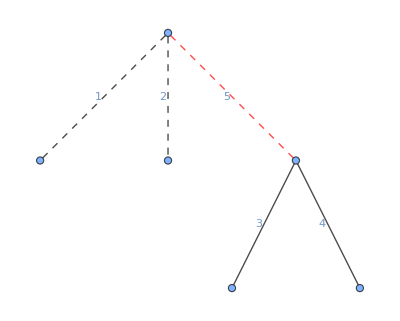
```mathematica
AsymmetricHiggsQ[{{-Graphics-,{"S","S","F","F","NB"},{{1,2,5},{3,4,5}}},{"H","H","L","L",{{0},{0},{0,0},{2},1}}}]
```

False

Another example, but this one would not lead to a non-derivative operator because the output is True:

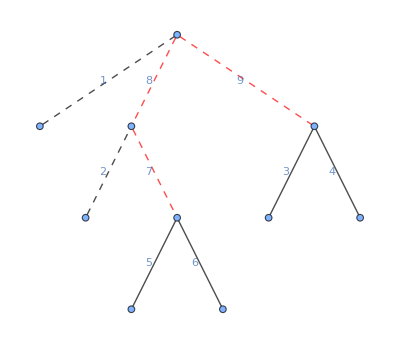
```mathematica
AsymmetricHiggsQ[{{-Graphics-,{"S","S","F","F","F","F","NB","NB","NB"},{{5,6,7},{2,7,8},{1,8,9},{3,4,9}}},{"H","H","dR","dR","Q","L",{{0},{0},{1,0},{0},-1/3},{{0},{0},{1,0},{1},1/6},{{0},{0},{1,0},{0},2/3}}}]
```

True

In this case it is easy to understand what is going on: 7 and 9 are SU(2)L singlets, so 1 and 2 -- the two Higgses -- have to form an SU(2) singlet as well, but that contraction is zero if the p8 propagator is just a constant. If we kept the momentum dependence of the p8 propagator the amplitude would not vanish, but would be described by a derivative operator. See main article for details.

A complicated case that allows for 2 different invariants at one vertex.  One of them is non-zero, the other zero. So, one way to couple Hc-Hc-p7-p8 to a singlet involves an anti-symmetric Hc pair and is therefore 0, but the other option is fine. As long as there is at least one non-zero amplitude, the underlying UV completion is valid for non-derivative operators:

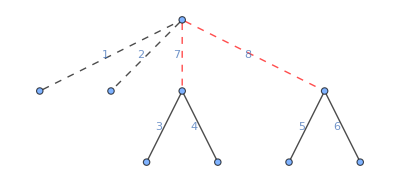
```mathematica
AsymmetricHiggsQ[{{-Graphics-,{"S","S","F","F","F","F","NB","NB"},{{3,4,7},{5,6,8},{1,2,7,8}}},{"Hc","Hc","uR","Q","L","uR",{{1},{1},{0,1},{1},5/6},{{1},{1},{1,0},{1},1/6}}}]
```

False

Okay, let’s use this on our previous list of 22 UV completions. Turns out 4 of those actually generate derivative operators (at mass dimension 10 or 11):

```mathematica
finallist=DeleteCases[fulllistNoDuplicates,x_/;AsymmetricHiggsQ[x]];
Length[finallist]
```

18

Here are the four cases that give vanishing amplitudes in the constant-propagator limit. In all cases one can easily track the SU(2) contractions and verify that the anti-Higgs pair is forced to couple to an SU(2) singlet, which is antisymmetric and thus gives a vanishing amplitude:

```mathematica
Complement[fulllistNoDuplicates,finallist]
```

{{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{H,Hc,Hc,dR,dR,ec,Q,{{0},{0},{1,0},{1},7/6},{{0},{0},{1,0},{0},5/3},{{0},{1},{1,0},{1},-5/6},{{0},{1},{1,0},{1},-5/6}}},{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{H,Hc,Hc,ec,dR,Q,dR,{{1},{1},{0,1},{1},-1/6},{{1},{1},{0,1},{0},1/3},{{1},{0},{0,0},{1},1/2},{{0},{1},{1,0},{1},-5/6}}},{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{Hc,Hc,H,dR,Q,ec,dR,{{1},{1},{1,0},{0},2/3},{{1},{1},{1,0},{1},1/6},{{0},{1},{1,0},{1},-5/6},{{1},{0},{1,0},{0},2/3}}},{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{Hc,Hc,H,ec,Q,dR,dR,{{0},{0},{0,1},{0},-2/3},{{0},{0},{0,1},{1},-7/6},{{1},{0},{0,0},{1},1/2},{{1},{0},{1,0},{0},2/3}}}}

After removing equivalent UV completions and cases that vanish due to Higgs asymmetry, one is left with the final list “finallist”, which can then be exported as needed. Notice that we do not export our UV completions in exactly this format, {{topology, uv completion 1}, {topology, uv completion 2},...}, because of the massive increase in file size due to the repetitive topology entries. Instead, we export our lists as {topology,{uv completion 1, uv completion 2,...}}. This is the format of the UV completions supplied by us.

Notice that one might wonder about amplitudes that vanish due to fermion asymmetries, similar to the Higgs asymmetry case. In our BNV cases, we checked that this does not happen up to d=15. We explain how to check for this in the next section, which requires a calculation of the amplitude.

## Calculating the amplitude

Function that calculates the “amplitude” (or expands the operator) of a given UV completion in the constant-propagator limit and setting masses and constants to 1. The purpose is not the overall prefactor but the symmetry under particle exchange. The code is essentially the same as for the Higgs asymmetry, but without throwing in random numbers for the external wavefunctions at the end:

```mathematica
amplitude[uvcompletion_]:=Module[{topology,vertex,vertexfactors={},newparticlelabels,newparticlelabelsbar,newparticlestates,newparticlestatesbar,vertexproduct,w,inv,particles,in,finalamplitude={}},
topology=uvcompletion[[1]];
particles=uvcompletion[[2]]/.InverseReplaceSMnames;
(*figure out which of the particles are internal and need to be integrated out. we get the labels of all new particles from topology, so {p3,p5,...}*)
newparticlelabels=ToExpression[StringJoin["p",IntegerString[#]]&/@Flatten[Join[Position[topology[[2]],"NB"],Position[topology[[2]],"NF"]]]];
(*and we also get p3bar, p5bar to distinguish incoming and outgoing internal particles:*);
newparticlelabelsbar=ToExpression[StringJoin["p",IntegerString[#],"bar"]&/@Flatten[Join[Position[topology[[2]],"NB"],Position[topology[[2]],"NF"]]]];
(*If there are no internal particles, we're looking at a simple 3 or 4-particle vertex; still give amplitude for convenience:*)
If[Length[newparticlelabels]==0,
vertex=1;
If[Length[topology[[3]][[vertex]]]==3,
(*3-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]]},{Conjugations->{False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];,
(*4-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],particles[[topology[[3,vertex,4]]]]},{Conjugations->{False,False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]],d->ToExpression[ToString[p]<>ToString[topology[[3,vertex,4]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];
];
Return[inv];
];
(*run over all the vertices in the diagram, except the last one, and calculate the full group invariants at each vertex, renaming the multiplets by particle labels p1, p2, p3 etc that match the labelling in the topology. We treat all but the last particle in each vertex as incoming, and the last one as outgoing (Conjugations -> True), following the same logic as in UVCompletions. We distinguish 3 and 4-particle vertices:*)
For[vertex=1,vertex<Length[topology[[3]]],vertex++,
If[Length[topology[[3]][[vertex]]]==3,
(*3-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]]},{Conjugations->{False,False,True}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]<>"bar"]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ", topology[[3]][[vertex]]]];
If[vertex==1,
(*for first vertex, vertexfactors = Invariants[...]*)
vertexfactors=inv;,
(*for all subsequent vertices, vertexfactors is updated to a nested list: {{inv(vertex1)[1],inv(vertex2)[1],...},{inv(vertex1)[2],inv(vertex2)[1],...} so that vertexfactors[[1]] collects one possible set of diagram invariants, vertexfactors[[2]] another, etc. *)
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];,
(*4-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],particles[[topology[[3,vertex,4]]]]},{Conjugations->{False,False,False,True}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]],d->ToExpression[ToString[p]<>ToString[topology[[3,vertex,4]]]<>"bar"]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ", topology[[3]][[vertex]]]];
If[vertex==1,
(*for first vertex, vertexfactors = Invariants[...]*)
vertexfactors=inv;,
(*for all subsequent vertices, vertexfactors is updated to a nested list: {{inv(vertex1)[1],inv(vertex2)[1],...},{inv(vertex1)[2],inv(vertex2)[1],...} so that vertexfactors[[1]] collects one possible set of diagram invariants, vertexfactors[[2]] another, etc. *)
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];
];
];
(*At the last vertex, all particles are incoming, otherwise same procedure, the group invariants for each vertex are added to the list vertexfactors:*)
vertex=Length[topology[[3]]];
If[Length[topology[[3]][[vertex]]]==3,
(*3-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]]},{Conjugations->{False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ", topology[[3]][[vertex]]]];
(*thread it into the non-empty vertexfactor list*);
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];,
(*4-particle vertex*)
inv=Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],particles[[topology[[3,vertex,4]]]]},{Conjugations->{False,False,False,False}}]/.{a->ToExpression[ToString[p]<>ToString[topology[[3,vertex,1]]]],b->ToExpression[ToString[p]<>ToString[topology[[3,vertex,2]]]],c->ToExpression[ToString[p]<>ToString[topology[[3,vertex,3]]]],d->ToExpression[ToString[p]<>ToString[topology[[3,vertex,4]]]]};
If[MemberQ[inv,0],Print["Vanishing vertex! ",topology[[3]][[vertex]]]];
If[Length[inv]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];
(*thread it into the non-empty vertexfactor list*);
vertexfactors=Flatten[Table[Flatten[{x,y}],{x,vertexfactors},{y,inv}],1];
];
(*for each internal particle, say p3, we now read off all multiplet components from their occurance in vertexfactors, so this gives all spin and gauge multiplet states of p3, and then same for p3bar*);
newparticlestates=Values[GroupBy[DeleteDuplicates[Cases[vertexfactors,Alternatives@@(#[___]&/@newparticlelabels),All]],Head]];
newparticlestatesbar=newparticlestates/.Thread[newparticlelabels -> newparticlelabelsbar];
(*the most important part: we multiply all vertex factors, which is similar to the diagram amplitude since propagators are constants in our non-derivative ansatz:*);
For[in=1,in<=Length[vertexfactors],in++,
vertexproduct=Apply[Times,vertexfactors[[in]]];
(*in this amplitude, each new-particle state shows up once as p3[...] and once as p3bar[...]. The propagator connects these two if they have the same argument. So, integrating out p3 boils down to taking the derivative of the amplitude with respect to p3[x] and p3bar[x], and sum over x. Then we do the same for all other new particles:*);
For[w=1,w<=Length[newparticlestates],w++,
vertexproduct=Sum[D[vertexproduct,newparticlestates[[w]][[i]],newparticlestatesbar[[w]][[i]]],{i,Length[newparticlestates[[w]]]}]
];
(*the final vertexproduct only depends on the external SM states, i.e. the internal particles have been integrated out, properly taking care of the group contractions.*)
AppendTo[finalamplitude,vertexproduct]
];
(*Final output is a list: an amplitude for each possible way to have an invariant diagram. *)
Return[finalamplitude]
]
```

Example:

```mathematica
amplitude[{{-Graphics-,{"F","F","F","F","NB"},{{1,2,5},{3,4,5}}},{"uR","uR","dR","eR",{{0},{0},{0,1},{0},4/3}}}]
```

{(-(3^(1/4) p1[1,2,3,1] p2[1,1,2,1])/(√2)+(3^(1/4) p1[1,2,2,1] p2[1,1,3,1])/(√2)+(3^(1/4) p1[1,1,3,1] p2[1,2,2,1])/(√2)-(3^(1/4) p1[1,1,2,1] p2[1,2,3,1])/(√2)) (p3[1,2,1,1] p4[1,1,1,1]-p3[1,1,1,1] p4[1,2,1,1])+((3^(1/4) p1[1,2,3,1] p2[1,1,1,1])/(√2)-(3^(1/4) p1[1,2,1,1] p2[1,1,3,1])/(√2)-(3^(1/4) p1[1,1,3,1] p2[1,2,1,1])/(√2)+(3^(1/4) p1[1,1,1,1] p2[1,2,3,1])/(√2)) (p3[1,2,2,1] p4[1,1,1,1]-p3[1,1,2,1] p4[1,2,1,1])+(-(3^(1/4) p1[1,2,2,1] p2[1,1,1,1])/(√2)+(3^(1/4) p1[1,2,1,1] p2[1,1,2,1])/(√2)+(3^(1/4) p1[1,1,2,1] p2[1,2,1,1])/(√2)-(3^(1/4) p1[1,1,1,1] p2[1,2,2,1])/(√2)) (p3[1,2,3,1] p4[1,1,1,1]-p3[1,1,3,1] p4[1,2,1,1])}

This amplitude depends on the external particle wavefunctions or multiplet components; p4[a,b,c,d] stands for the “eR” field, a is the component under the Lorentz (SU(2))_left, which is always 1 here since eR is in the singlet representation of this group; b is the component under (SU(2))_right, which takes values from 1 to 2; c stands for (SU(3))_color, so this is again just fixed to 1 for eR, same for d, which labels (SU(2))_L. So eR only has two components, p4[1, 1, 1, 1] and p4[1, 2, 1, 1]. Other objects, esp. Q, are more complicated. To check whether an amplitude is symmetric or antisymmetric under particle exchange, it is more convenient to treat this as a function of p1,...p4:

```mathematica
amp=Function[{p1,p2,p3,p4},Evaluate[amplitude[{{-Graphics-,{"F","F","F","F","NB"},{{1,2,5},{3,4,5}}},{"uR","uR","dR","eR",{{0},{0},{0,1},{0},4/3}}}]]];
```

The amplitude is symmetric under p1 <-> p2 exchange, i.e. exchange of the two uR fields:

```mathematica
amp[p1,p2,p3,p4]-amp[p2,p1,p3,p4]//Simplify
```

{0}

Notice that we don’t have Grassmann numbers here, so an antisymmetric fermion amplitude shows up as symmetric, basically all Young tableaux are transposed. The above result then says that the amplitude is actually antisymmetric under uR exchange, and would thus vanish if both uR came from the same generation. This is of course known, the S1-tilde leptoquark we are looking at here has an antisymmetric coupling to up quarks.
Using this amplitude code one can check for arbitrary particle exchange symmetries in a given UV completion.

We can also confirm that this “amplitude” is just a linear combination of GroupMath’s Invariants for that operator, as it should be. For the case above there are two different contractions of the operator,

```mathematica
Invariants[group,{"uR","uR","dR","eR"}/.InverseReplaceSMnames]//Length
```

2

and our amplitude is proportional to the second one:

```mathematica
(Invariants[group,{"uR","uR","dR","eR"}/.InverseReplaceSMnames][[2]]/.a->p1/.b->p2/.c->p3/.d->p4)/(amp[p1,p2,p3,p4][[1]])//Simplify
```

1

In general, each amplitude is proportional to some linear combination of the GroupMath invariants Inv[1],...,Inv[n]:

```mathematica
example={{-Graphics-,{"S","S","S","F","F","F","F","NB","NB","NF","NF"},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{"Hc","Hc","H","Q","ec","dR","dR",{{0},{0},{0,1},{0},-2/3},{{0},{0},{0,1},{1},-7/6},{{1},{0},{1,0},{0},-1/3},{{1},{0},{0,0},{1},3/2}}}
(*just pick the first entry in amplitude, can do the same for each other entry of course:*)
amp=amplitude[example][[1]]/.{p1->a,p2->b,p3->c,p4->d,p5->e,p6->f,p7->g,p8->h}//Simplify;
inv=Invariants[group,example[[2]][[1;;Count[VertexDegree[example[[1,1]]],1]]]/.InverseReplaceSMnames]//Simplify;
coeffs=Array[x,Length[inv]];
lincomb=coeffs.inv;
states=DeleteDuplicates[Flatten[Values[GroupBy[DeleteDuplicates[Cases[inv,Alternatives@@(#[___]&/@{a,b,c,d,e,f,g,h}),All]],Head]]]];
sol=Solve[Table[0==Simplify[(amp-lincomb)/.Thread[states -> Rationalize[RandomReal[{-4,4},Length[states]],1/100]]],{j,Length[coeffs]}],coeffs,Reals]
If[Simplify[(amp-lincomb)/.sol[[1]]]==0,Print["Our UV completion = ",Sum[(x[j]/.sol[[1]])"Inv"[j],{j,Length[coeffs]}]],Print["Can't find linear combintion of invariants that match our amplitude."]]
```

{{-Graphics-,{S,S,S,F,F,F,F,NB,NB,NF,NF},{{6,7,8},{1,8,9},{2,4,10},{3,5,11},{9,10,11}}},{Hc,Hc,H,Q,ec,dR,dR,{{0},{0},{0,1},{0},-2/3},{{0},{0},{0,1},{1},-7/6},{{1},{0},{1,0},{0},-1/3},{{1},{0},{0,0},{1},3/2}}}

{{x[1]→-(√3)/2,x[2]→1/2}}

Our UV completion = -1/2 √3 Inv[1]+Inv[2]/2

Instead of the GroupMath operator basis one can also use others, e.g. the Warsaw basis for d=6 operators.

## Pretty diagrams

A function to display a UV completion in a fairly pretty way including the charge flow, dropping chirality for convenience. The graph is rotated to avoid overlapping labels, but this does not always solve the problem. Notice that the output is no longer a Graph object but just a graphic.

```mathematica
PrettyUVGraph[uvcompletion_]:=Module[{DropChirality,transformListGeneral,fullgraph,edgeLabels,newEdgeLabels},

DropChirality[expr_]:=expr /. {(*Scalar (S):{0},{0}*){{0}, {0}, rest___} :> {"S",rest},(*Fermion (F):{0},{1} or {1},{0}*){{0}, {1},rest___} :> {"F", rest},{{1}, {0}, rest___} :> {"F",rest},(*Vector (V):{1},{1}*){{1}, {1}, rest___} :> {"V", rest}};

transformListGeneral[list_]:=list/. {s_String,aa_,bb_,cc_}:>Subscript[s, Replace[RepName[{SU3,SU2,U1},{aa,bb,cc}],CircleTimes[a_,b_,c_]:>Row[{"(",a,", ",b,", ",c,")"}]]];

fullgraph=FullParticleDiagram[DropChirality[uvcompletion/.{"Q"->"Q_L","L"->"L_L","uR"->"u_R","dR"->"d_R","eR"->"e_R","NR"->"N_R","Qc"->"(Q̄)_L","Lc"->"(L̄)_L","uc"->"(ū)_R","dc"->"(d̄)_R","ec"->"(ē)_R","Nc"->"(N̄)_R","H"->"H","Hc"->"H̄"}]];
(*Extract current edge labels*)
edgeLabels=EdgeLabels/. AbsoluteOptions[fullgraph,EdgeLabels];

(*Replace only the labels of the form {"S",{0,0},{1},1/2}*)
newEdgeLabels=edgeLabels/. s:{x:("S"|"F"|"V"),__}:>transformListGeneral[s];

Return[TreePlot[SetProperty[fullgraph,EdgeLabels->newEdgeLabels],Right,VertexStyle->Black,VertexSize->Tiny,PlotStyle->Thick,EdgeLabelStyle->Directive[15]]]
]
```

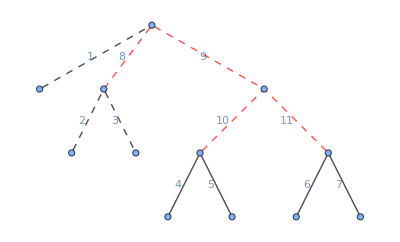
```mathematica
PrettyUVGraph[{{-Graphics-,{"S","S","S","F","F","F","F","NB","NB","NB","NB"},{{2,3,8},{1,8,9},{4,5,10},{6,7,11},{9,10,11}}},{"H","Hc","Hc","ec","Q","dR","dR",{{0},{0},{0,0},{2},-1},{{0},{0},{0,0},{1},-1/2},{{0},{0},{1,0},{1},7/6},{{0},{0},{0,1},{0},-2/3}}}]
```

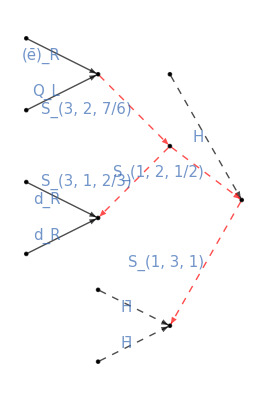

## Importing our UV files

Download the UV completions from https://julian-heeck.github.io/BNV/ and simply import whichever case you’re interested in. The UV completions are sorted into folders of mass dimension, and amount of baryon and lepton number violation. For example, UV_Dim8_1B_1L contains all UV completions for d=8 operators with B=1 and L=1. Inside each folder, one finds .wl files of a certain topology-operator combination, e.g. UV_Dim8_1B_1L_T3_O7.wl, which contains UV completions for topology 3 and operator 7. Each file looks something like this:

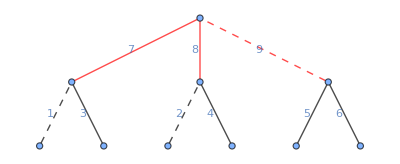
```mathematica
import={{-Graphics-,{"S","S","F","F","F","F","NF","NF","NB"},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{{"H","H","dR","dR","Q","L","F[8]","F[8]","S[4]"},{"H","H","dR","Q","dR","L","F[8]","F[14]","V[1]"},{"H","H","dR","Q","dR","L","F[8]","F[6]","V[1]"},{"H","H","dR","L","dR","Q","F[8]","F[4]","Vc[2]"},{"H","H","dR","L","dR","Q","F[8]","F[1]","Vc[2]"},{"H","H","Q","L","dR","dR","F[14]","F[4]","Sc[3]"},{"H","H","Q","L","dR","dR","F[6]","F[1]","Sc[3]"}}};
```

the first entry is the topology, the second entry is the list of UV completions, using the particle names F[8], S[5], V[1] from our article. Vc[2] means the antiparticle of V[2]. We provide simple lookup tables for the new particle quantum numbers, contained in the folder “newparticles”:

```mathematica
NewScalars=Join@@Table[Import[NotebookDirectory[]<>"newparticles/NewScalars_Dim"<>ToString[d]<>".wl"],{d,6,15}];
NewVectors=Join@@Table[Import[NotebookDirectory[]<>"newparticles/NewVectors_Dim"<>ToString[d]<>".wl"],{d,6,15}];
NewFermions=Join@@Table[Import[NotebookDirectory[]<>"newparticles/NewFermions_Dim"<>ToString[d]<>".wl"],{d,6,15}];

LookupNewParticle[x_]:=Module[{particle},
particle=StringCases[x,RegularExpression["([A-Za-z]+)\\[(\\d+)\\]"]:>{"$1",ToExpression["$2"]}];
If[Length[particle]!=0,
If[particle[[1,1]]=="S",Return[NewScalars[[particle[[1,2]]]]]];
If[particle[[1,1]]=="V",Return[NewVectors[[particle[[1,2]]]]]];
If[particle[[1,1]]=="F",Return[NewFermions[[particle[[1,2]]]]]];
If[particle[[1,1]]=="Sc",Return[FlattenAt[{NewScalars[[particle[[1,2]]]][[1]],ConjugateRep[NewScalars[[particle[[1,2]]]][[2;;4]]]},-1]]];
If[particle[[1,1]]=="Vc",Return[FlattenAt[{NewVectors[[particle[[1,2]]]][[1]],ConjugateRep[NewVectors[[particle[[1,2]]]][[2;;4]]]},-1]]];
If[particle[[1,1]]=="Fc",Return[FlattenAt[{NewFermions[[particle[[1,2]]]][[1]],ConjugateRep[NewFermions[[particle[[1,2]]]][[2;;4]]]},-1]]];
,Return[x]];
];

GetParticleName[particleRep_]:=Module[{DropChirality,particle,name},
DropChirality[expr_]:=expr /. {(*Scalar (S):{0},{0}*){{0}, {0}, rest___} :> {"S",rest},(*Fermion (F):{0},{1} or {1},{0}*){{0}, {1},rest___} :> {"F", rest},{{1}, {0}, rest___} :> {"F",rest},(*Vector (V):{1},{1}*){{1}, {1}, rest___} :> {"V", rest}};
(*if representation is of the form Subscript[SU(2), left] Subscript[xSU(2), right] x Subscript[SU(3), color] Subscript[xSU(2), L] xU Subscript[(1), Y] we convert to chirality-blind output, e.g. {"F",{1,0},{1},1/2}*);
Which[
Length[particleRep]==5,particle=DropChirality[RepNaming[particleRep]],
Length[particleRep]==4&&StringQ[particleRep[[1]]],particle=RepNaming[particleRep],
True,Print["unknown rep format"];Return[];
];
Which[
particle[[1]]=="S",name=StringJoin["S[",ToString[FirstPosition[NewScalars,particle][[1]]],"]"],
particle[[1]]=="F",name=StringJoin["F[",ToString[FirstPosition[NewFermions,particle][[1]]],"]"],
particle[[1]]=="V",name=StringJoin["V[",ToString[FirstPosition[NewVectors,particle][[1]]],"]"],
True,Print["unknown rep format"];Return[];
];
If[name=="S[NotFound]"||name=="F[NotFound]"||name=="V[NotFound]",Print["particle not in list"];Return[];];
Which[RepNaming[particleRep]==particleRep,Return[name],RepNaming[particleRep]==ConjugateRep[particleRep],Return[ConjugateRep[name]],True,"unknown rep"];
]
```

For example:

```mathematica
LookupNewParticle["F[5]"]
LookupNewParticle["Fc[5]"]
%//RepNaming
```

{F,{1,0},{0},-1/3}

{F,{0,1},{0},1/3}

{F,{1,0},{0},-1/3}

In reverse, we can also check the particle name corresponding to a set of quantum numbers, which corresponds simply to the position in our list:

```mathematica
GetParticleName[{"F",{1,0},{0},-1/3}]
GetParticleName[{"F",{0,1},{0},1/3}]
```

F[5]

Fc[5]

If you’re only interested in UV completions involving one particular internal particle (and its antiparticle), just look for them in the list:

```mathematica
whichUVyouwant="S[3]";
{import[[1]],Select[import[[2]],MemberQ[#,whichUVyouwant,{1,Infinity}]||MemberQ[#,ConjugateRep[whichUVyouwant],{1,Infinity}]&]}
```

{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{{H,H,Q,L,dR,dR,F[14],F[4],Sc[3]},{H,H,Q,L,dR,dR,F[6],F[1],Sc[3]}}}

One can easily bring it back to the same {{topology, uv completion 1},{topology, uv completion 2},..} format we used earlier:

```mathematica
convertedimport=Table[{import[[1]],import[[2,j]]},{j,Length[import[[2]]]}]
```

{{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,dR,Q,L,F[8],F[8],S[4]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,Q,dR,L,F[8],F[14],V[1]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,Q,dR,L,F[8],F[6],V[1]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,L,dR,Q,F[8],F[4],Vc[2]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,L,dR,Q,F[8],F[1],Vc[2]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,Q,L,dR,dR,F[14],F[4],Sc[3]}},{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,Q,L,dR,dR,F[6],F[1],Sc[3]}}}

and this even works with PrettyUVGraph (in that it changes the arrow directions of all Sc, Fc, and Vc):

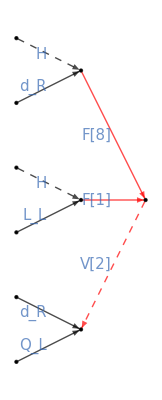

```mathematica
convertedimport[[5]]//PrettyUVGraph
```

Sometimes it is useful to read off the operator from the UV completion and then collect its properties, namely baryon number B, lepton number L, mass dimension d, number of fermions F, and number of scalars S:

```mathematica
(*takes an operator like {"Q","Q","Q","L"} and returns a list {baryon number, lepton number, operator dimension, number of fermions, number of scalars}, e.g. BLd[{"Q","Q","Q","L"}] = {1,1,6,4,0}}*)
BLdFS[operator_]:=Module[{baryons,antibaryons,leptons,antileptons,scalars},
baryons=Count[operator,"Q"]+Count[operator,"uR"]+Count[operator,"dR"];
antibaryons=Count[operator,"Qc"]+Count[operator,"uc"]+Count[operator,"dc"];
leptons=Count[operator,"L"]+Count[operator,"eR"]+Count[operator,"NR"];
antileptons=Count[operator,"Lc"]+Count[operator,"ec"]+Count[operator,"Nc"];
scalars=Count[operator,"H"]+Count[operator,"Hc"];
If[Length[operator]!=(baryons+antibaryons+leptons+antileptons+scalars),Print["unexpected fields in operator"]];
{1/3(baryons-antibaryons),(leptons-antileptons),3/2(baryons+antibaryons+leptons+antileptons)+scalars,baryons+antibaryons+leptons+antileptons,scalars}
]
```

Try it out on our imported UV file:

```mathematica
convertedimport[[5]];
%[[2]][[1;;Count[%[[1,2]],"S"|"F"]]]
BLdFS[%]
```

{H,H,dR,L,dR,Q}

{1,1,8,4,2}

So the operator H H dR L dR Q has B=1, L=1, d=8, 4 fermions, and 2 scalars.

Notice that our UV completions have been stripped of their chirality structure, i.e. whether internal fermions are left- or right-handed. Since all fermions are massive and we enforce a chirality flip on each internal fermion line, both chiralities are present and this omission seems innocuous. The only reason to keep the chirality structure is to check for AsymmetricHiggsQ -- which is unnecessary since we have already removed UV completions with AsymmetricHiggsQ == True -- or to calculate the amplitude. We provide the function ReconstructQuantumNumbers to restore the chirality information by going through the diagram and flipping fermion chiralities as necessary to get valid vertices:

```mathematica
ReconstructQuantumNumbers[x_]:=RestoreUVChirality[{x[[1]],Map[LookupNewParticle,x[[2]]]}];

RestoreUVChirality[uvcompletion_]:=Module[{vertex,vertexfactors={},vertexproduct,Hlabels,Hclabels,totalantisymlist={},w,inv,k,particles,in,FlipChirality,RewriteInUVCodeConvention,topology},(*Just flips the Lorentz SU(2)xSU(2) indices,i.e.the chirality*)

FlipChirality[list_]:={list[[2]],list[[1]],list[[3]],list[[4]],list[[5]]};

RewriteInUVCodeConvention[x_]:=With[{h=x[[1]]},Join[Which[h==="F",{{0},{1}},h==="S",{{0},{0}},h==="V",{{1},{1}},MatchQ[h,{{_Integer..}..}],h,True,{h}],Rest[x]]];

topology=uvcompletion[[1]];

(*convert our chirality-stripped uv completion to the notation including chirality.For external particles,this is unique;for internal particles,we don't know if they should be chirality flipped*);
particles=Map[RewriteInUVCodeConvention,uvcompletion[[2]]/. InverseReplaceSMnames];
(*run over all the vertices in the diagram,except the last one,and calculate the full group invariants at each vertex,renaming the multiplets by particle labels p1,p2,p3 etc that match the labelling in the topology.We treat all but the last particle in each vertex as incoming,and the last one as outgoing (Conjugations->True),following the same logic as in UVCompletions.We distinguish 3 and 4-particle vertices:*)For[vertex=1,vertex<Length[topology[[3]]],vertex++,(*3-particle vertex*)If[Length[topology[[3]][[vertex]]]==3,(*check if the vertex is invariant,i.e.Length[inv]!=0,if yes,all good and move on*)Which[Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,True}}]]!=0,Null,(*if that didn't work,try chirality-flipping the last particle and see if the vertex is invariant now.If yes,that is the right thing to do and we update the quantum numbers in "particles"*)Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],FlipChirality[particles[[topology[[3,vertex,3]]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,True}}]]!=0,particles[[topology[[3,vertex,3]]]]=FlipChirality[particles[[topology[[3,vertex,3]]]]],(*if nothing worked print error message*)True,Print["couldn't construct invariant 3-vertex ",topology[[3]][[vertex]]]];,(*4-particle vertex*)(*check if the vertex is invariant,i.e.Length[inv]!=0,if yes,all good and move on*)Which[Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],particles[[topology[[3,vertex,4]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,False,True}}]]!=0,Null,(*if that didn't work,try chirality-flipping the last particle and see if the vertex is invariant now.If yes,that is the right thing to do and we update the quantum numbers in "particles"*)Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],FlipChirality[particles[[topology[[3,vertex,4]]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,False,True}}]]!=0,particles[[topology[[3,vertex,4]]]]=FlipChirality[particles[[topology[[3,vertex,4]]]]],(*if nothing worked print error message*)True,Print["couldn't construct invariant 4-vertex ",topology[[3]][[vertex]]]];];];
(*At the last vertex,all particles are incoming and we've already corrected all quantum numbers in "particles",so the vertices should come out invariant,otherwise same procedure,the group invariants for each vertex are added to the list vertexfactors:*)vertex=Length[topology[[3]]];
If[Length[topology[[3]][[vertex]]]==3,(*3-particle vertex*)If[Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,False}}]]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];,(*4-particle vertex*)If[Length[Invariants[group,{particles[[topology[[3,vertex,1]]]],particles[[topology[[3,vertex,2]]]],particles[[topology[[3,vertex,3]]]],particles[[topology[[3,vertex,4]]]]}/. InverseReplaceSMnames,{Conjugations->{False,False,False,False}}]]==0,Print["Non-existing vertex! ",topology[[3]][[vertex]]]];];
Return[{uvcompletion[[1]],Join[Table[particles[[k]]/. ReplaceSMnames,{k,1,Count[topology[[2]],"S"]+Count[topology[[2]],"F"]}],(*external particles,match back to SM names*)Table[particles[[k]],{k,Count[topology[[2]],"S"]+Count[topology[[2]],"F"]+1,Length[topology[[2]]]}]]}];]
```

ReconstructQuantumNumbers returns a fully valid UV completion that can be used in any of the previous functions, e.g. amplitude or PrettyUVGraph:

{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,Q,dR,L,F[8],F[6],V[1]}}

{{-Graphics-,{S,S,F,F,F,F,NF,NF,NB},{{1,3,7},{2,4,8},{5,6,9},{7,8,9}}},{H,H,dR,Q,dR,L,{{0},{1},{1,0},{1},1/6},{{1},{0},{1,0},{0},2/3},{{1},{1},{1,0},{1},-5/6}}}

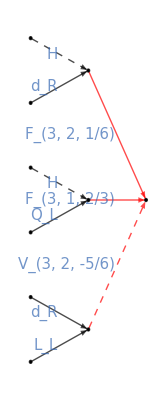

```mathematica
convertedimport[[3]]
%//ReconstructQuantumNumbers
(*%//amplitude*)
%//PrettyUVGraph
```

This should be sufficient to work with the provided UV completions. In addition, we’re providing significantly stripped down versions of UV completions in .dat format, again to be downloaded from https://julian-heeck.github.io/BNV/. For example, importing “UV_Dim8_1B_1L_T2.dat” gives

```mathematica
{{"O_{8,(1,1)}^{1}","S[3]S[5]S[4]","V[1]V[2]V[8]","V[3]V[1]V[2]"},{"O_{8,(1,1)}^{2}","V[1]V[2]V[8]","V[3]V[1]V[2]","S[1]S[11]S[4]"},{"O_{8,(1,1)}^{3}","S[1]S[11]S[4]","V[1]V[2]V[8]","V[3]V[1]V[2]"},{"O_{8,(1,1)}^{4}","S[4]S[4]S[13]","S[5]S[4]S[4]","S[2]S[5]S[4]","S[2]S[2]S[5]","S[4]S[4]S[12]","S[11]S[4]S[4]","S[2]S[11]S[4]","S[2]S[2]S[11]"},{"O_{8,(1,1)}^{5}","S[2]S[5]S[4]","S[2]S[2]S[5]","V[1]V[1]V[8]","V[3]V[1]V[1]","V[2]V[2]V[8]","V[3]V[2]V[2]","V[2]V[2]V[5]","V[4]V[2]V[2]","V[1]V[1]V[7]","V[6]V[1]V[1]","S[2]S[11]S[4]","S[2]S[2]S[11]"},{"O_{8,(1,1)}^{6}","V[1]V[1]V[8]","V[3]V[1]V[1]","S[2]S[11]S[4]","S[2]S[2]S[11]","S[2]S[5]S[4]","S[2]S[2]S[5]","V[1]V[1]V[7]","V[6]V[1]V[1]"},{"O_{8,(1,1)}^{7}","S[1]S[1]S[11]","S[2]S[2]S[5]","S[2]S[2]S[11]","S[1]S[1]S[10]"},{"O_{8,(1,1)}^{8}","V[2]V[2]V[5]","V[4]V[2]V[2]","S[2]S[11]S[4]","S[2]S[2]S[11]","S[2]S[5]S[4]","S[2]S[2]S[5]","V[2]V[2]V[8]","V[3]V[2]V[2]"},{"O_{8,(1,1)}^{9}","V[1]V[2]V[8]","V[3]V[1]V[2]","S[3]S[5]S[4]"},{"O_{8,(1,1)}^{10}","S[2]S[2]S[5]","S[3]S[3]S[5]","S[3]S[3]S[6]","S[2]S[2]S[11]"}}
```

which contains UV completions for all operators with topology T2, stripping away the external particles (which are encoded in the operator names “O_{8,(1,1)}^{j}”) and flipping all internal antiparticles to particles, i.e. Sc[3] -> S[3]. This is very compact but sufficient for some tasks such as counting how often a new particle appears in a given mass dimension.